```mathematica
(*Calculations for Lemma 4.2 Case 1*)
```

```mathematica
Simplify[(1/(2+p))*(1/(2+p))*(p/(2+p))^p+(1/(2+p))*(1/(2+p))^p*(p/(2+p))+(1/(2+p))^p*(1/(2+p))*(p/(2+p))]
```

(2 p (1/(2+p))^p+(p/(2+p))^p)/(2+p)^2

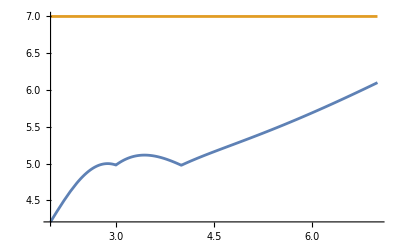

```mathematica
Plot[{(3/(2*E)*Max[{1/2^(p-1),1/2^3((p-1)/p)^(p-4)}]+Max[{1/2^p,1/2^3(p/(p+1))^(p-3)}])/((p+2)*(2 p (1/(2+p))^p+(p/(2+p))^p)/(2+p)^2),7},{p,2,7}]
```

```mathematica
NMaximize[(3/(2*E)*Max[{1/2^(p-1),1/2^3((p-1)/p)^(p-4)}]+Max[{1/2^p,1/2^3(p/(p+1))^(p-3)}])/((p+2)*(2 p (1/(2+p))^p+(p/(2+p))^p)/(2+p)^2),p>=2&&p<=7,{p}]
```

{6.10037,{p→7.}}

```mathematica
(*Calculations for Lemma 4.2 Case 2*)
```

```mathematica
Block[{p=8},Simplify[(3E)/2*((p-1)^2+3)/((p-1)^2-1)(((p+2)(p-3))/(p-2)^p+(p+2)/(p-2)*1/E)+(2-p+p^2)/((-2+p)(1+p))(((p+2)(p-2))/(p-1)^(p+1)+(p+2)/(p-1)*1/E)*E^2]]
```

65/24+(72163555 ⅇ)/47029248+(580 ⅇ^2)/363182463

```mathematica
N[65/24+(72163555 ⅇ)/47029248+(580 ⅇ^2)/363182463]
```

6.87939

```mathematica
(*Calculations for Lemma 4.4 Base case*)
```

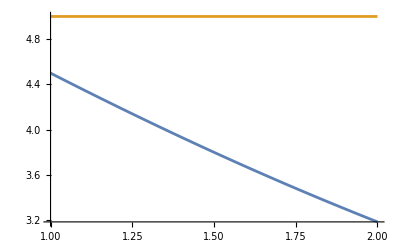

```mathematica
Plot[{(p(1/2)^(2-p)(1/9)^(p-1)+1/4^(p-1))/((p+2)(1/3)^(p+1)),5},{p,1,2}]
```

```mathematica
NMaximize[(p(1/2)^(2-p)(1/9)^(p-1)+1/4^(p-1))/((p+2)(1/3)^(p+1)),p>=1&&p<=2,{p}]
```

{4.5,{p→1.}}